```mathematica
SetDirectory["/home/ebg/Documents/2_Latex/CAMDA"]
```

/home/ebg/Documents/2_Latex/CAMDA

```mathematica
(*SetDirectory["F:\\CAMDA"]*=
```

```mathematica
dat00=Import["CAMDA(z).dat","Table"];
nOTU=Length[dat00]-1
```

298

```mathematica
borrar=Transpose[dat00];
nCTY=Length[borrar]-1
```

365

```mathematica
dat=Table[dat00[[i,j]],{i,1,5},{j,1,nCTY+1}];
TableForm[dat]
```

ID | AKL | AKL | AKL | AKL | AKL | AKL | AKL | AKL | AKL | AKL | AKL | AKL | AKL | AKL | BER | BER | BER | BER | BER | BER | BER | BER | BER | BER | BER | BER | BER | BER | BER | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | BOG | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | LIS | LIS | LIS | LIS | LIS | LIS | LIS | LIS | LIS | LIS | LIS | LIS | LIS | LIS | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | SAC | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | BAL | BAL | BAL | BAL | BAL | BAL | BAL | BAL | BAL | BAL | BAL | BAL | BAL | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DEN | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | DOH | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | ILR | MIN | MIN | MIN | MIN | MIN | MIN | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | NYC | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAN | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | SAO | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | TOK | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | VIE | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH | ZRH
469__Genus | 1170550 | 39068 | 13322 | 2454 | 5321 | 1643 | 2541 | 2100 | 75073 | 2723 | 2125 | 1998 | 1753 | 2635 | 243163 | 86190 | 140580 | 179169 | 203527 | 4936726 | 10364 | 25485 | 6997 | 10475 | 660030 | 9336 | 7024 | 63359 | 496521 | 301687 | 196754 | 289210 | 390036 | 161759 | 324815 | 290397 | 824878 | 1287948 | 188500 | 257180 | 544650 | 612466 | 577602 | 297167 | 7050 | 3916 | 9570 | 5800 | 7817 | 25454 | 16537 | 157748 | 4715 | 5914 | 65955 | 7147 | 118631 | 8128 | 9683 | 3137 | 6830 | 26189 | 8746 | 5577 | 13256 | 5232 | 10029 | 26593 | 11286 | 15775 | 15513 | 7640 | 12598 | 15563 | 15579 | 17100 | 21336 | 12487 | 17547 | 2127316 | 24944 | 2547370 | 34892 | 16753 | 1269017 | 11983 | 232713 | 17862 | 3518408 | 17152 | 32499 | 10178 | 474913 | 2577037 | 286146 | 2893 | 2407617 | 176543 | 5077 | 132633 | 548667 | 581346 | 164264 | 122954 | 1537113 | 3266 | 3863 | 3395 | 162111 | 5501955 | 124408 | 5315615 | 64608 | 10129994 | 260194 | 118141 | 7552255 | 68231 | 250418 | 5032264 | 12882331 | 106897 | 11395316 | 9510858 | 88844 | 1144917 | 21553 | 216539 | 649192 | 103436 | 48897 | 3532172 | 822078 | 484383 | 2745 | 3014 | 3840 | 30491 | 7018 | 22751 | 2731 | 12440 | 10737 | 23001 | 2874 | 3752 | 3911 | 26919 | 3581 | 84264 | 22259 | 91751 | 138079 | 177318 | 106504 | 216519 | 103077 | 94181 | 290779 | 61028 | 54847 | 130779 | 136463 | 17349 | 33089 | 270940 | 70769 | 267953 | 24244 | 46032 | 98909 | 93835 | 120209 | 133573 | 4117 | 2932 | 12909 | 6803 | 12813 | 23632 | 64300 | 2149 | 4450 | 5028 | 4511 | 7914 | 3610 | 2726 | 4266 | 1354 | 1519 | 6087 | 2477 | 978 | 2088 | 4763 | 920 | 952 | 1934 | 9622 | 4176 | 1811 | 3906 | 520 | 1508 | 7282 | 3445 | 1462 | 1375 | 5148 | 34573 | 10313 | 183035 | 16931 | 9650 | 32137 | 4836 | 8991 | 5029 | 5750 | 67064 | 9522 | 19864 | 21504 | 11658 | 830198 | 7866 | 121877 | 78490 | 19583 | 14234 | 8151 | 88876 | 62384 | 13032 | 25541 | 28887 | 90923 | 20287 | 28930 | 37139 | 1315 | 978 | 4978 | 2319 | 1197 | 1880 | 10202 | 10886 | 4448 | 5334 | 28018 | 7182 | 3611 | 24806 | 3900 | 3842 | 7358 | 5707 | 19439 | 367790 | 7393 | 1884 | 6511 | 10776 | 5934 | 4412 | 2058 | 1803 | 776 | 2743 | 11282 | 5320 | 1509 | 2657 | 635 | 420 | 1042 | 2707 | 1231 | 4927 | 8185 | 3713 | 995 | 6073 | 2604 | 42164 | 1573 | 2143 | 1000 | 1164 | 6572 | 3568 | 1761 | 18317 | 6930 | 671 | 74789 | 310 | 6833 | 6741 | 8070 | 546 | 619 | 6534 | 2552 | 874 | 13190 | 4915 | 20732 | 38390 | 1228 | 5671 | 1697 | 1294 | 1707 | 394 | 1362 | 39328 | 22164 | 19931 | 4381 | 2724 | 3084 | 2462 | 4177 | 4413 | 26766 | 2084 | 886 | 1633 | 1374 | 3260 | 13635 | 5648 | 4849 | 6596 | 6247 | 2895 | 20472 | 38991 | 12841 | 6603 | 8707 | 15493 | 27765 | 12937 | 119397 | 7663 | 33594 | 13221 | 2765 | 189412 | 3457 | 45521 | 21576 | 22038 | 2961 | 19502 | 30648 | 12592 | 24567 | 16876 | 58666 | 24028
861445__Genus | 345835 | 1420 | 209 | 209 | 5555 | 64 | 78 | 99 | 61952 | 116 | 139 | 120 | 120 | 111 | 56105 | 3867 | 19336 | 8682 | 10193 | 3747 | 956 | 1318 | 279 | 341 | 588 | 821 | 669 | 5130 | 17225 | 40933 | 76429 | 69564 | 22847 | 93286 | 19547 | 47532 | 75880 | 317568 | 25297 | 21256 | 33371 | 9963 | 15141 | 22028 | 79 | 56 | 147 | 58 | 266 | 589 | 97 | 125 | 89 | 96 | 114 | 45 | 159 | 154 | 107 | 39 | 207 | 95 | 118 | 217 | 58 | 50 | 355 | 222 | 233206 | 323 | 242 | 192 | 238 | 345 | 278 | 244 | 270 | 281 | 273 | 679 | 476 | 326 | 296 | 1950 | 595 | 205 | 461 | 1273 | 469 | 1344 | 189 | 1640 | 894 | 131 | 2649 | 103 | 135 | 106 | 103 | 37 | 227 | 28 | 1806 | 45 | 104 | 354 | 56421 | 28 | 22719 | 60563 | 14053 | 235339 | 15562 | 10645 | 50013 | 27617 | 15827 | 12860 | 5931 | 37039 | 83087 | 23558 | 22119 | 24021 | 16711 | 21315 | 3724 | 6219 | 20856 | 14966 | 10846 | 6741 | 46969 | 31898 | 566 | 202 | 269 | 1887 | 793 | 911 | 236 | 889 | 1485 | 1587 | 269 | 300 | 234 | 252 | 327 | 355 | 374 | 2138 | 2524 | 1523 | 2372 | 3236 | 1363 | 1923 | 2999 | 1315 | 1491 | 3598 | 70057 | 385 | 885 | 2107 | 1129 | 1577 | 2425 | 797 | 3519 | 1820 | 3482 | 2388 | 250 | 215 | 2990 | 343 | 425 | 527 | 1799 | 93 | 182 | 225 | 313 | 2046 | 360 | 524 | 142 | 269 | 166 | 733 | 203 | 136 | 102 | 250 | 135 | 133 | 181 | 367 | 231 | 98 | 204 | 104 | 149 | 268 | 217 | 78 | 165 | 129 | 4758 | 292 | 388 | 270 | 151 | 1771 | 101 | 220 | 89 | 236 | 869 | 339 | 573 | 216 | 53 | 1680 | 137 | 424 | 167 | 75 | 101 | 201 | 517 | 578 | 1187 | 436 | 208 | 766 | 309 | 274 | 319 | 278 | 88 | 580 | 88 | 42 | 180 | 298 | 748 | 461 | 1118 | 13482 | 397 | 289 | 25528 | 476 | 272 | 5302 | 623 | 34620 | 396 | 1811 | 308 | 487 | 1467 | 545 | 549 | 305 | 218 | 32 | 910 | 85 | 671 | 412 | 388 | 55 | 35 | 400 | 381 | 172 | 1533 | 1067 | 844 | 26 | 1087 | 104 | 52 | 84 | 29 | 9 | 15 | 45 | 162 | 17 | 271 | 146 | 7 | 585 | 12 | 33 | 98 | 114 | 11 | 31 | 36 | 30 | 13 | 187 | 44 | 146 | 445 | 76 | 166 | 103 | 63 | 38 | 15 | 84 | 474 | 93 | 146 | 123 | 93 | 64 | 79 | 164 | 400 | 139 | 196 | 55 | 24 | 29 | 203 | 761 | 202 | 185 | 496 | 312 | 163 | 5134 | 1490 | 580 | 228 | 584 | 10932 | 860 | 1126 | 2417 | 306 | 2025 | 220 | 109 | 2830 | 109 | 328 | 2098 | 2344 | 181 | 1971 | 1716 | 6531 | 3824 | 926 | 21621 | 1858
34062__Genus | 552 | 1319 | 156 | 76 | 96 | 41 | 1355 | 95 | 121 | 89 | 110 | 609 | 564 | 56 | 84028 | 32281 | 72221 | 34165 | 112138 | 27843 | 11962 | 5963 | 6749 | 10389 | 3637 | 3460 | 2307 | 31548 | 329184 | 90984 | 53106 | 140759 | 63113 | 76071 | 92944 | 110767 | 178525 | 56738 | 78697 | 57696 | 137660 | 33851 | 82835 | 73397 | 356 | 303 | 749 | 295 | 956 | 2772 | 570 | 3076 | 406 | 382 | 604 | 282 | 871 | 629 | 797 | 228 | 573 | 612 | 566 | 57835 | 300 | 273 | 39485 | 18718 | 6361 | 8435 | 9686 | 6770 | 10052 | 7411 | 8200 | 5882 | 9213 | 6879 | 7330 | 1244 | 899 | 651 | 812 | 1847603 | 1046 | 607 | 822 | 1277 | 1312 | 864664 | 581 | 1250 | 978 | 590 | 331 | 61357 | 214 | 260 | 94042 | 269 | 147 | 76 | 823 | 84 | 68 | 1951 | 96435 | 9744 | 47146 | 78733 | 121018 | 86218 | 10837 | 81904 | 77014 | 28622 | 85224 | 36559 | 17566 | 43017 | 53803 | 37500 | 50724 | 54526 | 20281 | 80544 | 6070 | 30637 | 39770 | 28128 | 20245 | 24785 | 54743 | 31694 | 194 | 221 | 279 | 1719 | 579 | 1867 | 463 | 533 | 839 | 9145 | 140 | 470 | 294 | 179 | 286 | 174 | 32721 | 284453 | 182186 | 130599 | 250895 | 90000 | 87132 | 209079 | 110160 | 96612 | 103030 | 418781 | 51788 | 29166 | 33246 | 95390 | 73855 | 104886 | 26726 | 4905 | 279318 | 124617 | 339126 | 271095 | 2447 | 1625 | 7967 | 3502 | 17061 | 8171 | 4465 | 1499 | 658 | 1992 | 4860 | 4488 | 1623 | 786 | 553 | 255 | 636 | 2044 | 1459 | 798 | 330 | 1205 | 754 | 149 | 994 | 1465 | 5478 | 304 | 958 | 78 | 828 | 1135 | 4550 | 1040 | 23233 | 3419 | 84540 | 9082 | 71397 | 1140 | 5021 | 257402 | 3122 | 7592 | 4212 | 1350 | 77620 | 2337 | 20188 | 6444 | 817 | 7869 | 649 | 5180 | 15677 | 1471 | 806 | 1521 | 3286 | 1888 | 1437 | 13264 | 7747 | 23968 | 26870 | 19483 | 25585 | 472 | 372 | 965 | 413 | 431 | 799 | 2489 | 5334 | 1483 | 4595 | 12131 | 2957 | 2568 | 15384 | 2519 | 7201 | 3129 | 4042 | 11771 | 306 | 3111 | 2768 | 6824 | 4769 | 6739 | 8652 | 823 | 415 | 145 | 815 | 551 | 976 | 193 | 947 | 205 | 158 | 288 | 352 | 303 | 1042 | 367 | 10208 | 216 | 1215 | 919 | 1879 | 421 | 886 | 215 | 160 | 1241 | 998 | 350 | 1414 | 697 | 101 | 88395 | 453 | 966 | 3270 | 833 | 240 | 299 | 3537 | 272 | 147 | 1126 | 3241 | 21393 | 52097 | 9452 | 25413 | 1994 | 84 | 424 | 42 | 2072 | 30658 | 3541 | 10909 | 17968 | 15007 | 8901 | 2148 | 18741 | 11953 | 39227 | 5742 | 50 | 1553 | 391 | 3483 | 8650 | 767 | 1421 | 3756 | 8052 | 7782 | 16493 | 5944 | 6949 | 4255 | 1714 | 11034 | 10440 | 7797 | 63530 | 5560 | 5710 | 15441 | 1969 | 112178 | 2394 | 47210 | 20094 | 5585 | 1249 | 6785 | 11601 | 4587 | 5409 | 4003 | 13831 | 5408
316__Genus | 1827 | 1626 | 2180 | 1664 | 7557 | 1170 | 1876 | 2681 | 3761 | 1728 | 10985 | 2289 | 2161 | 2982 | 1187492 | 216671 | 47824 | 384495 | 78678 | 16925688 | 1125 | 1321 | 1126 | 1071 | 759 | 607 | 721 | 206745 | 199645 | 88434 | 104745 | 56673 | 188229 | 76770 | 128907 | 160261 | 71484 | 838061 | 44311 | 91564 | 175418 | 101993 | 85389 | 104730 | 84 | 81 | 221 | 171 | 358 | 2039 | 404 | 102 | 105 | 163 | 2706 | 84 | 4767 | 254 | 163 | 60 | 197 | 683 | 157 | 121 | 184 | 85 | 5709 | 11615 | 8041 | 18006 | 32616 | 15429 | 12123 | 14077 | 8699 | 16744 | 16791 | 9460 | 16690 | 13765242 | 450141 | 25034060 | 133503 | 40219 | 24455743 | 15822072 | 1630200 | 39958 | 28119624 | 43555 | 30168873 | 133905 | 21937498 | 27580624 | 328733 | 10906 | 1379398 | 1995391 | 21551 | 1286168 | 190425 | 1906550 | 1342053 | 1220770 | 11590 | 11199 | 10399 | 14094 | 67102 | 38972 | 33753 | 51864 | 27466 | 32334 | 48943 | 26226 | 25289 | 37463 | 14580 | 32013 | 86865 | 45258 | 34547 | 110140 | 25064 | 24533 | 11894 | 17367 | 24436 | 51568 | 25166 | 1930937 | 41660 | 75417 | 1492 | 1580 | 1595 | 3537 | 2528 | 1519 | 1446 | 1683 | 1623 | 2228 | 1688 | 2275 | 2567 | 1174 | 2012 | 1805 | 49937 | 160638 | 52151 | 44425 | 79965 | 39191 | 26778 | 184006 | 23835 | 36837 | 76588 | 39799 | 161654 | 22656 | 20527 | 66937 | 32263 | 30193 | 37464 | 90596 | 27030 | 436170 | 456595 | 77839 | 661 | 423 | 1741 | 749 | 1787 | 1613 | 7508 | 195 | 537 | 856 | 1506 | 3554 | 792 | 661 | 858 | 326 | 211 | 1738 | 985 | 1538 | 257 | 2143 | 1573 | 131 | 359 | 369 | 3470 | 253 | 1846 | 74 | 312 | 357 | 3057 | 437 | 416 | 2061 | 1737 | 6842 | 255 | 3961 | 19715 | 88669 | 3621 | 6697 | 1923 | 7630 | 4565 | 3221 | 18898 | 20902 | 3850 | 73232 | 6732 | 103061 | 10398 | 6789 | 7474 | 8033 | 46876 | 100629 | 14478 | 17398 | 33025 | 72189 | 14526 | 13478 | 10817 | 2970 | 2520 | 3791 | 2711 | 1829 | 5020 | 1763 | 3062 | 1615 | 4007 | 6214 | 2088 | 1194 | 9413 | 1200 | 1378 | 7651 | 7735 | 8931 | 21022 | 2019 | 2218 | 9106 | 6817 | 3010 | 1806 | 1119 | 1291 | 121 | 542 | 2092 | 2534 | 339 | 257 | 1500 | 142 | 327 | 280 | 182 | 1899 | 1047 | 1813 | 525 | 1242 | 1265 | 297 | 591 | 1082 | 249 | 249 | 4396 | 638 | 877 | 732 | 530 | 343 | 326 | 101 | 544 | 15253 | 1081 | 117 | 193 | 983 | 3601 | 499 | 690 | 206 | 468 | 1056 | 354 | 524 | 652 | 177 | 734 | 41 | 403 | 1005 | 194 | 1138 | 1073 | 433 | 833 | 1505 | 352 | 776 | 746 | 574 | 122 | 489 | 190 | 824 | 1185 | 1940 | 499 | 2771 | 1184 | 607 | 4117 | 2378 | 1903 | 1218 | 2693 | 2823 | 783 | 1757 | 7545 | 883 | 2683 | 1129 | 832 | 5418 | 735 | 14259 | 9247 | 1943 | 418 | 2517 | 2769 | 2210 | 24184 | 2034 | 5680 | 3635

```mathematica
Length[Drop[dat[[1]],1]]
```

365

```mathematica
LAB=Drop[dat[[1]],1];
aux=Tally[LAB]
```

{{AKL,14},{BER,15},{BOG,15},{DEN,44},{DOH,27},{ILR,33},{LIS,14},{NYC,46},{SAC,16},{TOK,49},{BAL,13},{MIN,6},{SAN,16},{SAO,25},{VIE,16},{ZRH,16}}

```mathematica
nC=Length[aux]
```

16

```mathematica
II=nCTY;
JJ=nOTU;COL={Red,Blue,Green,Brown,Black,Pink,Gray,Magenta,Cyan,Orange,Yellow,LightBlue,LightPurple,LightBrown,LightOrange,LightRed};
```

```mathematica
dat0=Transpose[Drop[Transpose[Take[Drop[dat00,1],JJ]],1]];
```

```mathematica
x=Transpose[dat0];
Length[Transpose[x]]
```

298

```mathematica
X0=Table[Log[x[[i,j]]+1.0],{i,1,II},{j,1,JJ}];
TableForm[X0];
```

```mathematica
X=X0;
```

```mathematica
c=Correlation[X];
MatrixForm[c];
```

```mathematica
ei=Eigenvalues[c];
```

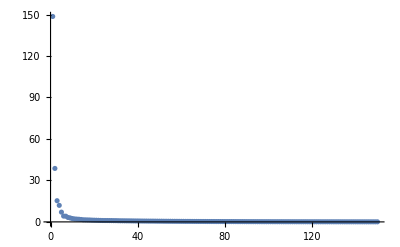

```mathematica
ee=Table[ei[[i]],{i,1,Min[JJ,150]}];
ListPlot[ee,PlotRange->All]
```

```mathematica
Sum[ei[[i]],{i,1,100}]/Sum[ei[[i]],{i,1,JJ}]
```

0.980184

```mathematica
U=-Transpose[Eigenvectors[c]];
MatrixForm[U];
```

```mathematica
z=-X.U;
```

```mathematica
tam=Round[II*0.75]
```

274

```mathematica
NEi=nOTU;
L=Table[Table[z[[i,j]],{j,1,NEi}],{i,1,II}];dcl=Table[L[[i]]->LAB[[i]],{i,1,II}];
```

```mathematica
Ltrai=RandomSample[dcl,tam];
Ltest=Complement[dcl,Ltrai];
```

```mathematica
NEiR=80;
LtraiR=Table[Take[Ltrai[[i,1]],NEiR]->Ltrai[[i,2]],{i,1,Length[Ltrai]}];LtestR=Table[Take[Ltest[[i,1]],NEiR]->Ltest[[i,2]],{i,1,Length[Ltest]}];CL=Classify[LtraiR, Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
sum=0;
Do[If[CL[LtestR[[i,1]]]==LtestR[[i,2]],sum=sum+1],{i,1,Length[LtestR]}];
N[sum/Length[LtestR]]
```

0.956044

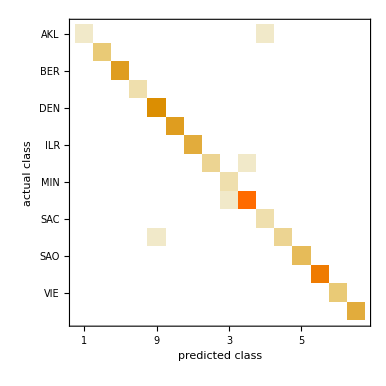

```mathematica
ClassifierMeasurements[CL,LtestR,"ConfusionMatrixPlot"]
```

```mathematica
ClassifierMeasurements[CL,LtestR,{"Accuracy"}]
```

{0.956044}

```mathematica
auxGB=GatherBy[dcl,Last];
```

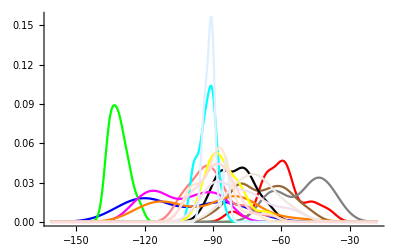

```mathematica
For[r=1,r<=nC,r++,
lf[r]=Table[auxGB[[r,i,1,1]],{i,1,aux[[r,2]]}]];SmoothHistogram[Table[lf[i],{i,1,nC}],PlotRange->All,PlotStyle->COL]
```

```mathematica
COL[[4]]
```

RGBColor[0.6, 0.4, 0.2]

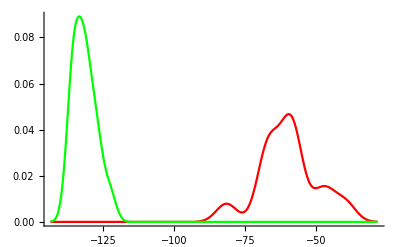

```mathematica
aa=1;
bb=3;
SmoothHistogram[{lf[aa],lf[bb]},PlotRange->All,
PlotStyle->{COL[[aa]],COL[[bb]]}]
```

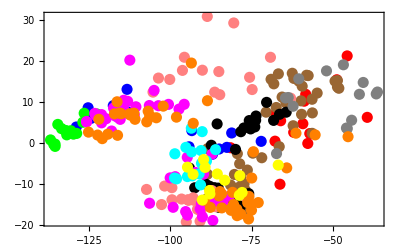

```mathematica
For[r=1,r<=nC,r++,
lf[r]=Table[{auxGB[[r,i,1,1]],auxGB[[r,i,1,2]]},{i,1,aux[[r,2]]}]];
ListPlot[Table[lf[r],{r,1,11}],Frame->True,PlotStyle->Table[{COL[[i]],PointSize[0.02]},{i,1,11}],Axes->False,PlotRange->All]
```

```mathematica
For[r=1,r<=nC,r++,
lf[r]=Table[{auxGB[[r,i,1,1]],auxGB[[r,i,1,2]],auxGB[[r,i,1,3]]},{i,1,aux[[r,2]]}]];
ListPointPlot3D[Table[lf[r],{r,1,nC}],PlotRange->All,PlotStyle->Table[{COL[[i]],PointSize[0.02]},{i,1,11}]]
```

-Graphics3D-

```mathematica
NEi=70;
L=Table[Table[z[[i,j]],{j,1,NEi}],{i,1,II}];dcl=Table[L[[i]]->LAB[[i]],{i,1,II}];tt=25;
(*Print[ProgressIndicator[Dynamic[k/tt]]];*)
Monitor[Do[
Ltrai=RandomSample[dcl,tam];
Ltest=Complement[dcl,Ltrai];
CL=Classify[Ltrai,Method->"LogisticRegression"];
sum=0;
Do[If[CL[Ltest[[i,1]]]==Ltest[[i,2]],sum=sum+1],{i,1,Length[Ltest]}];
vP[k]=N[sum/Length[Ltest]],{k,1,tt}];VPnuevo=Table[vP[k],{k,1,tt}],k];
mean=Mean[VPnuevo]
```

0.922637

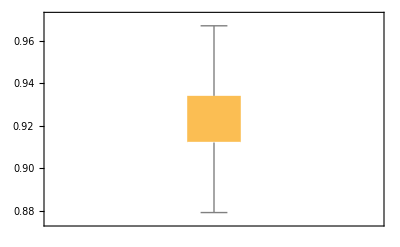

```mathematica
BoxWhiskerChart[VPnuevo]
```

```mathematica
HH=10;
Monitor[Do[
NEi=30+10*h;
L=Table[Table[z[[i,j]],{j,1,NEi}],{i,1,II}];dcl=Table[L[[i]]->LAB[[i]],{i,1,II}];
tt=100;
Do[
Ltrai=RandomSample[dcl,tam];
Ltest=Complement[dcl,Ltrai];
CL=Classify[Ltrai,Method->"LogisticRegression"];
sum=0;
Do[If[CL[Ltest[[i,1]]]==Ltest[[i,2]],sum=sum+1],{i,1,Length[Ltest]}];
VP[h,k]=N[sum/Length[Ltest]],{k,1,tt}];
VPnuevo=Table[VP[h,k],{k,1,tt}];
qq=Sum[ei[[i]],{i,1,NEi}]/Sum[ei[[i]],{i,1,JJ}];
sc[h]={NEi,qq,Mean[VPnuevo]},{h,1,HH}],h]
```

```mathematica
TT=Table[Table[VP[h,k],{k,1,tt}],{h,1,HH}];
```

```mathematica
TTaux=Import["TTz1.dat","Table"];
TTjoin=Join[TTaux,Transpose[TT]];Length[Transpose[TTjoin][[1]]]
```

500

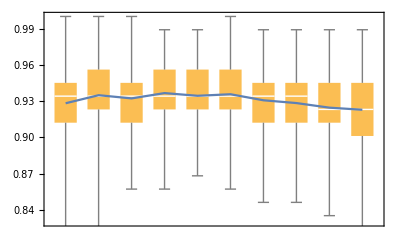

```mathematica
mTT=Table[Mean[Transpose[TTjoin][[h]]],{h,1,HH}];
g1=ListPlot[mTT,Joined->True];g2=BoxWhiskerChart[Transpose[TTjoin]];Show[g2,g1,PlotRange->{0.83,1}]
```

```mathematica
SC3=Table[{sc[h][[1]],sc[h][[2]],mTT[[h]]},{h,1,HH}];
TableForm[SC3]
```

40 | 0.913416 | 0.928176
50 | 0.932623 | 0.934835
60 | 0.947376 | 0.932198
70 | 0.958684 | 0.936593
80 | 0.967582 | 0.934352
90 | 0.974752 | 0.935626
100 | 0.980184 | 0.930637
110 | 0.984489 | 0.92833
120 | 0.98797 | 0.924527
130 | 0.990755 | 0.922791

```mathematica
Export["TTz1.dat",TTjoin]
```

TTz1.dat